```mathematica
(*Wykresy 3d*)

(*Plot3D*)
Plot3D[Sin[x] Cos[y],{x,-5Pi,2 Pi},{y,-2 Pi,2 Pi},Mesh->None,ColorFunction->None,ColorFunction->"Monochrome", Boxed->False,Axes->True,Axes->{"x","y","z"}]
```

-Graphics3D-

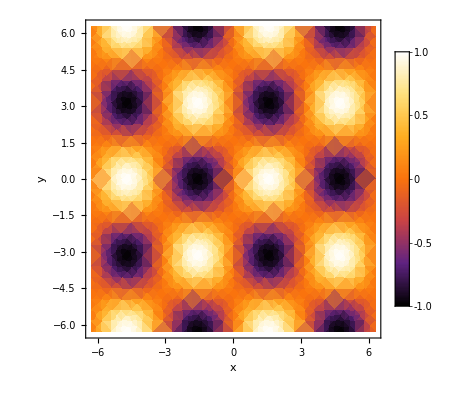

-Graphics3D-

```mathematica
(*DensityPlot*)
DensityPlot[Sin[x]*Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},PlotRange->All,ColorFunction->"SunsetColors",FrameLabel->{"x","y"},PlotLegends->Automatic,ColorFunction->"Rainbow"]
Plot3D[Sin[x]*Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},PlotRange->All,AxesLabel->{"x","y","f(x,y)"},ContourStyle-> 12,ColorFunction->"Rainbow", Boxed->False]
```

```mathematica
(*ParametricPlot3D*)
ParametricPlot3D[{Cos[t]*Sin[t],Sin[t]*Cos[u],Sin[u]},{t,0,2 Pi},{u,-Pi,Pi},PlotRange->All,Axes->None,Boxed->False,ViewVector->{5,5,2},ViewAngle->0.3,ImageSize->Large,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
(*Plot3D*)
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
(*ListPlot3D*)
```

```mathematica
ListPlot3D[Table[{x=RandomReal[{-1,1}],y=RandomReal[{-1,1}],Sqrt[1-x^2-y^2]},{1000}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
(*ListPointPlot3D*)
ListPointPlot3D[Table[Sin[i]Cos[j],{i,-5,5,.25},{j,-5,5,.25}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Table[(4Pi-t){Cos[t+s Pi/2],Sin[t+s Pi/2],0}+{0,0,2t},{t,0,4Pi,.1}],{s,4}],Filling->Bottom,ColorFunction->"Rainbow",BoxRatios->Automatic,FillingStyle->Directive[LightGreen,Thick,Opacity[.1]]]
```

-Graphics3D-

(-13. | 295.
-10. | 166.
-7. | 73.
-4. | 16.
-1. | -5.
2. | 10.
5. | 61.
8. | 148.)

-Graphics3D-

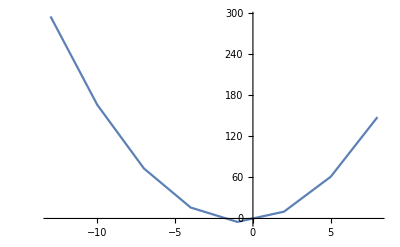

Plot3D[{2 x^2+3 x-4},{x,-13,10},Boxed→False]

{{-13.,295.},{-10.,166.},{-7.,73.},{-4.,16.},{-1.,-5.},{2.,10.},{5.,61.},{8.,148.}}

```mathematica
(*zadanie 1b edytowane do ListPlot3D*)
lw = {};
For[x=-13.0, x≤10,x+=3,AppendTo[lw,{N[x],2x^2+3x-4}];]
MatrixForm[lw]
ListPlot3D[lw,Boxed->False, Axes->True,AxesLabel->{"x","y","z"}]
ListLinePlot[lw]
Plot3D[{2x^2+3x-4}, {x, -13, 10}, Boxed->False]
({{-13., 295.}, {-10., 166.}, {-7., 73.}, {-4., 16.}, {-1., -5.}, {2., 10.}, {5., 61.}, {8., 148.}})
```